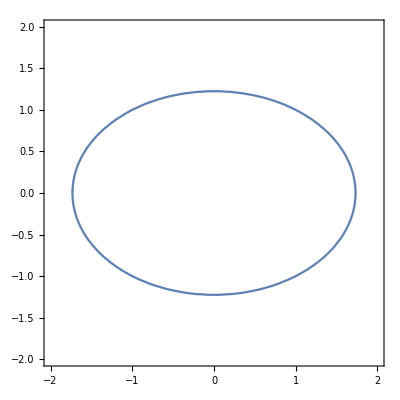

```mathematica
(*Задание 1*)
(*Построить график эллипса X^2+2*Y^2=3, используя ContourPlot[] пакета математки*)
AbsScaleX1=2;
AbsScaleY1=2;
ContourPlot[x^2+2*y^2==3,{x,-AbsScaleX1,AbsScaleX1},{y,-AbsScaleY1,AbsScaleY1}]
```

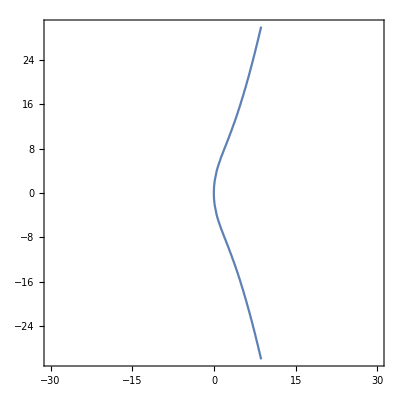

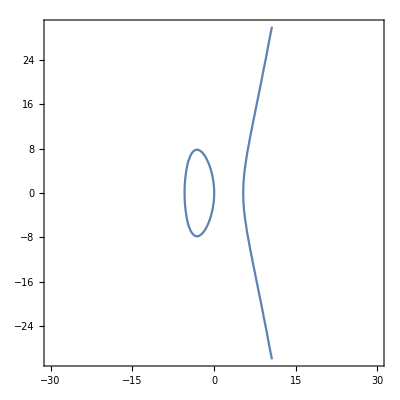

```mathematica
(*Задание 2*)
(*В поле рациональных чисел построить графики эллиптических кривых Y^2=X^3+a*X+b для положительного и отрицательного коэффициента a*)
a=29;
b=1;
p=31;
n=7;
AbsScaleX2=30;
AbsScaleY2=30;
ContourPlot[y^2==x^3+a*x+b,{x,-AbsScaleX2,AbsScaleX2},{y,-AbsScaleY2,AbsScaleY2}]
ContourPlot[y^2==x^3-a*x+b,{x,-AbsScaleX2,AbsScaleX2},{y,-AbsScaleY2,AbsScaleY2}]
```

```mathematica
(*Проверить выполенение условия гладкости кривой -16(4*a^3+27*b^2)≠0*)
-16*(4*a^3+27*b^2)≠0
```

True

```mathematica
(*Проверить, является ли заданный в правой части уравнения многочлен неприводимым, используя функцию Factor[]*)
Factor[x^3+a*x+b]==x^3+a*x+b
```

True

```mathematica
(*Задание 3*)
(*Проверить выполнение условия гладкости кривой в GF(p)*)
```

```mathematica
Mod[4*a^3+27*b^2,83]≠0
```

True

```mathematica
(*Определить число точек заданной кривой в поле GF(p)... *)
Clear[x,y]; 
Flatten[Table[ Solve[ {y^2== x^3+a x + b, x==u, Modulus==p}],{u, 0, p-1}] ,1];
g1={x,y}/.Flatten[Table[ Solve[ {y^2== x^3-a x + b, x==u, Modulus==p}],{u, 0, p-1}] ,1];
```

```mathematica
Length[g1]
```

62

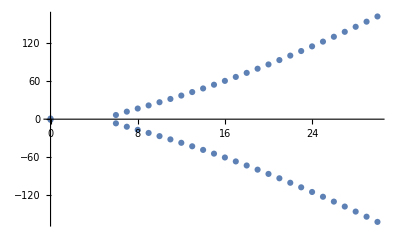

```mathematica
(*... и построить точеченый график*)
ListPlot[g1]
```

```mathematica
(*Задание 4*)
(*Сложить две точки, принадлежащие заданной эллиптической кривой, зафиксировать полученный результат на точеченом графике*)
(*Операцию сложения можно выполнить, используя следующий программный модуль*)
(*При использовании данного модуля следует учитывать,что он реализует сложение точек эллиптических кривых вида: y^2=x^3+ax^2+bx+c*)
```